{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

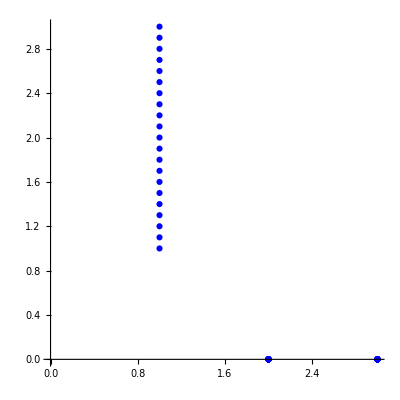

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.5,3.,0,0},{2.30665,2.9,0,0},{2.08133,2.8,0,0},{1.8293,2.7,0,0},{1.55778,2.6,0,0},{1.2757,2.5,0,0},{0.992908,2.4,0,0},{0.719046,2.3,0,0},{0.462526,2.2,0,0},{0.229794,2.1,0,0},{0.0250805,2.,0,0},{-0.149426,1.9,0,0},{-0.293168,1.8,0,0},{-0.406739,1.7,0,0},{-0.491451,1.6,0,0},{-0.54902,1.5,0,0},{-0.581361,1.4,0,0},{-0.590486,1.3,0,0},{-0.578483,1.2,0,0},{-0.547539,1.1,0,0},{-0.5,1.,0,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution_ode/psi_ode.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution_ode/psi_ode.csv

```mathematica
(*write w==0 to csv file*)
```

```mathematica
tabw=Table[{0,tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/w_ode.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/w_ode.csv

```mathematica
(*write sigma from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/sigma_ode.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/sigma_ode.csv

```mathematica
(*write z from ODE to csv file*)
```

```mathematica
tabz=Table[{z[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/z_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/z_ode.csv

```mathematica
(*write omega=z' from ODE to csv file*)
```

```mathematica
tabω=Table[{z'[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/omega_ode.csv

```mathematica
(*write mu=H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/solution-ode/mu_ode.csv